Sketch for better understanding

0.221472

(-0.354356 Sin[4.42945 t]-0.5 Cos[θ[t]] Sin[ϕ[t]] θ'[t]-0.5 Cos[ϕ[t]] Sin[θ[t]] ϕ'[t])^2

0.5 ((-0.708712 Sin[8.85889 t]+0.5 Sin[θ[t]] θ'[t])^2+(-0.354356 Sin[4.42945 t]-0.5 Cos[θ[t]] Sin[ϕ[t]] θ'[t]-0.5 Cos[ϕ[t]] Sin[θ[t]] ϕ'[t])^2+(-0.354356 Sin[4.42945 t]+0.5 Cos[θ[t]] Cos[ϕ[t]] θ'[t]-0.5 Sin[θ[t]] Sin[ϕ[t]] ϕ'[t])^2)

(19.62-12.5568 Cos[8.85889 t]) Sin[θ[t]]+Cos[4.42945 t] Cos[θ[t]] (-3.1392 Cos[ϕ[t]]+3.1392 Sin[ϕ[t]])+0.221472 θ'[t]-0.5 Sin[2 θ[t]] ϕ'[t]^2+1. θ''[t]

(0.221472+1. Sin[2 θ[t]] θ'[t]) ϕ'[t]+Sin[θ[t]] (Cos[4.42945 t] (3.1392 Cos[ϕ[t]]+3.1392 Sin[ϕ[t]])+1. Sin[θ[t]] ϕ''[t])

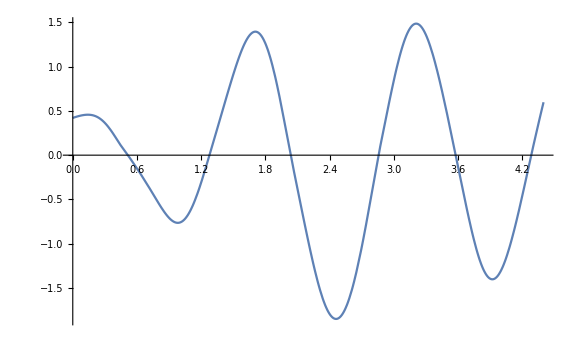

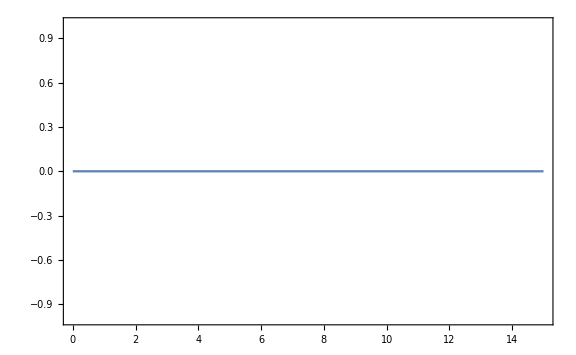

```mathematica
(*If you want to change the reverse colour format go to Format-> StyleSheet-> ReverseColour *)


SetOptions[$FrontEnd,PrintingStyleEnvironment->"Working"] 
(*SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]*)
ClearAll["Global`*"] 



Subscript[t, end]=1000;                        (* max time for the independent variable in ND Solve in s*)



l=0.5;                             (* Length of pendulum l*)
m=1.0;                          (*Mass at end of Pendulum in kg*)
g=9.81;                            (*Gravitational Acceleration in m/s^2*)


Subscript[ω, n]= Sqrt[g/l];          (*Frequency for Excitation close to Natural Frequency*)
Subscript[Ω, u]= 4.429446918;                              (*Frequency for Excitation for Coordinate System in Direction of u in 1/s*)
Subscript[Ω, v]= 4.429446918;                              (*Frequency for Excitation for Coordinate System in Direction of v in 1/s*)
Subscript[Ω, w]=2* 4.429446918;                        (*Frequency for Excitation for Coordinate System in Direction of w in 1/s*)


Subscript[U, 0]=0.08;                            (*Amplitude u in m   If[t<5,0.1,0]*)
Subscript[V, 0]=0.08;                           (*Amplitude v in m*)
Subscript[W, 0]=0.08;                              (*Amplitude w in m*) 


(*   (*Switiching off excitation after a defined time *)
Subscript[U, 0]=If[t<5,0.1,0];                            (*Amplitude u in m   If[t<5,0.1,0]*)
Subscript[V, 0]=If[t<5,0.1,0];                           (*Amplitude v in m*)
Subscript[W, 0]=If[t<5,0.1,0];                              (*Amplitude w in m*)     *)

(*Passive Damping*)

Subscript[ζ, θ] =0.025;                                 (*Damping coefficient no unit *)
Subscript[ζ, ϕ] =0.025;                                  (*Damping coefficient no unit*)

Subscript[C, θ] =2*Subscript[ζ, θ]*Subscript[ω, n]                    (*Damping θ in 1/s*)
Subscript[C, ϕ]=2*Subscript[ζ, ϕ]*Subscript[ω, n];                      (*Damping ϕ in 1/s*)





(*Torque Induced Rotations*)
Subscript[λ, θ]=0.0;                                    (* Static torque load in m*)
Subscript[λ, ϕ]=0.0;                                    (* Static torque load in m*)


Subscript[Ω, θ]=0.0;                                            (*Static Torque Frequency in Nm*)
Subscript[Ω, ϕ]=0.0;                                               (*Static Torque Frequency in Nm*)

(*Active power take off*)

Subscript[T, θ]=0.0;                                    (*Torque take off in Nm  swicht on with delay If[t<10,0.0,0.2]*)
Subscript[T, ϕ]=0.0;                                      (*Torque take off in Nm*)
(*Initial conditions   *)
icthe=0.42;           (*θ[0]*)
icphi=0.42;                       (*ϕ[0]*)
dicthe=0.42;                          (*θ'[0]*)
dicphi=0.42;                       (*ϕ'[0]*)

(*Kinematics *)
x[t]= -l*Sin[θ[t]]*Sin[ϕ[t]];
y[t]= l*Sin[θ[t]]*Cos[ϕ[t]];
z[t]= -l*Cos[θ[t]];                                           (*Center coordinate system at bottom if(l-lcos[θ] -> center at top*)

(*Excitations*)
u[t]=Subscript[U, 0]*Cos[Subscript[Ω, u]*t];
v[t]=Subscript[V, 0]*Cos[Subscript[Ω, v]*t];
w[t]=Subscript[W, 0]*Cos[Subscript[Ω, w]*t];

(* First time Derivatives of Cartesian Coordinates *)
x'[t]=D[x[t],t];
y'[t]=D[y[t],t];
z'[t]=D[z[t],t];
u'[t]=D[u[t],t];
v'[t]=D[v[t],t];
w'[t]=D[w[t],t];

(* Second time Derivatives of Cartesian Coordinates *)

x''[t]=D[x[t],{t,2}];
y''[t]=D[y[t],{t,2}];
z''[t]=D[z[t],{t,2}];
u''[t]=D[u[t],{t,2}];
v''[t]=D[v[t],{t,2}];
w''[t]=D[w[t],{t,2}];

(* Potential Energy *)

pot = m*g*z[t]+m*g*w[t];

(* Kinetic Energy *)

(* Pendelum without Absolute Frame Reference for checking purposes*)
Subscript[kin, 1]=(x'[t]+u'[t])^2
Subscript[kin, 2] =(y'[t]+v'[t])^2;
Subscript[kin, 3] = (z'[t]+w'[t])^2;
kinen = 0.5*m*(Subscript[kin, 1]+Subscript[kin, 2]+Subscript[kin, 3])



(* La Grange *)
(*respective to θ*)
Subscript[R, 11]=D[kinen ,θ'[t]];
Subscript[R, 21]=D[Subscript[R, 11],t];
Subscript[R, 31]=D[kinen ,θ[t]];
Subscript[R, 41]=D[pot,θ[t]];
eqn1=(Subscript[R, 21]-Subscript[R, 31]+Subscript[R, 41])/(m*l^2);

(*Damping*)
eqn1damp=eqn1+Subscript[C, θ]*θ'[t];


(*Torque Induced Rotations*)

eqn1torin=eqn1damp+((Subscript[λ, θ]*Cos[Subscript[Ω, θ]*t])/(m*l^2));

(*Active Power Take Off*)
eqn1powertake= eqn1torin +((Subscript[T, θ]*Sign[θ'[t]])/(m*l^2));

simpleqn1powertake=FullSimplify[eqn1powertake]

(*respective to ϕ*)
Subscript[R, 12]=D[kinen ,ϕ'[t]];
Subscript[R, 22]=D[Subscript[R, 12],t];
Subscript[R, 32]=D[kinen ,ϕ[t]];
Subscript[R, 42]=D[pot,ϕ[t]];
eqn2=(Subscript[R, 22]-Subscript[R, 32]+Subscript[R, 42])/(m*l^2);

(*Damping*)
eqn2damp=eqn2+Subscript[C, ϕ]*ϕ'[t];
(*Torque Induced Rotations*)

eqn2torin=eqn2damp+((Subscript[λ, ϕ]*Cos[Subscript[Ω, ϕ]*t])/(m*l^2));

(*Active Power Take Off*)

eqn2powertake= eqn2torin  +((Subscript[T, ϕ]*Sign[ϕ'[t]])/(m*l^2)) ; 
simpleqn2powertake=FullSimplify[eqn2powertake]



(*ND Solve of La Grange Equations*)

     

                        
s=NDSolve[{simpleqn1powertake==0,simpleqn2powertake==0,θ[0]==icthe,ϕ[0]==icphi,θ'[0]==dicthe,ϕ'[0]==dicphi},{θ,ϕ},{t,0,Subscript[t, end]},MaxSteps->∞]; 



(*Set file Path if file path is where your notebook is saved SetDirectory[NotebookDirectory[]]*)
SetDirectory["H:\\My Documents\\PhD\\1_Research\\Report\\20200316_Half_year\\photo_transfer\\"];

(*PTO Fourier Series*)
(*
Plot[Evaluate[-π/4(Sin[(θ'[t]*t/.s)]+1/3 Sin[(3θ'[t]*t/.s)]+1/5 Sin[(5θ'[t]*t/.s)])],{t,10,15},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic]
*)

Plot[θ[t]/. s,{t,0,4.4}]

Plot[Evaluate[{-(Subscript[T, θ] 4)/π(Sin[(θ'[t])]+1/3 Sin[(3θ'[t])]+1/5 Sin[(5θ'[t])])}/.s],{t,0,15},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic];
Plot[Evaluate[{-(Subscript[T, θ] 2)/π(ArcTan[(θ'[t]/0.01)])}/.s],{t,0,15},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic];


Plot[((-Subscript[T, θ])*(RealSign[θ'[t]/.s])),{t,0,15},
ImageSize ->Large,
Frame->True]
Plot[Evaluate[(θ'[t]/.s)],{t,0,15},Frame->True,FrameTicks->Automatic,ImageSize ->720,GridLines->Automatic,FrameLabel->{"time[s]","θ(t) [rad]"},LabelStyle->20,PlotPoints->200];


(*Plots θ and ϕ and their derivatives over time in DEG not in RAD*)

Plot[Evaluate[{θ[t],ϕ[t],w[t]}/.s],{t,0,50},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic];


Plot[Evaluate[(-θ[t]/.s)*Cos[ϕ[t]/.s]],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic];
Plot[Evaluate[(θ[t]/.s)*Sin[ϕ[t]/.s]],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic];
ParametricPlot[Evaluate[{θ[t]*Cos[ϕ[t]],θ[t]*Sin[ϕ[t]]}/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic];
(*
Plot[Evaluate[(θ[t]/.s)*(180/π)],{t,0,30},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{Style["time[s]",16],Style["θ(t) [Deg]",16]}]


*)
Plot[Evaluate[(θ[t]/.s)],{t,0,250},Frame->True,FrameTicks->Automatic,ImageSize ->720,GridLines->Automatic,FrameLabel->{"time[s]","θ(t) [rad]"},LabelStyle->20,PlotPoints->200];

Plot[Evaluate[(θ[t]/.s)],{t,0,250},Frame->True,FrameTicks->Automatic,ImageSize ->720,GridLines->Automatic,FrameLabel->{"time[s]","θ(t) [rad]"},LabelStyle->20,PlotPoints->200];

Plot[Evaluate[(θ'[t]/.s)],{t,0,250},Frame->True,FrameTicks->Automatic,ImageSize ->720,GridLines->Automatic,FrameLabel->{"time[s]","θ'(t) [rad/s]"},LabelStyle->20,PlotPoints->200];


pl1=Plot[Evaluate[(θ[t]/.s)*(180/π)],{t,0,200},PlotRange->{-100,100},Frame->True,FrameTicks->Automatic,ImageSize ->720,GridLines->Automatic,FrameLabel->{"time[s]","θ(t) [Deg]"},LabelStyle->20,PlotPoints->200];
Export["1_theta_displacement_time.pdf",pl1]; 
pl2=Plot[Evaluate[(ϕ[t]/.s)*(180/π)],{t,0,100},PlotRange->{-300,100},Frame->True,FrameTicks->Automatic,ImageSize ->720,GridLines->Automatic,FrameLabel->{"time[s]","ϕ(t) [Deg]"},LabelStyle->20];
Export["1_phi_displacement_time.pdf",pl2];

Plot[Evaluate[(θ'[t]/.s)*(180/π)],{t,0,30},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","θ̇(t) [Deg/s]"},LabelStyle->20];
Export["1_theta_acceleration_time.pdf",%];
Plot[Evaluate[(ϕ'[t]/.s)*(180/π)],{t,0,150},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","ϕ̇(t) [Deg/s]"},LabelStyle->20];


Plot[Evaluate[(θ''[t]/.s)*(180/π)],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","θ^(..)(t) [Deg/s^2]"},LabelStyle->20];
Plot[Evaluate[(ϕ''[t]/.s)*(180/π)],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","ϕ^(..)(t) [Deg/s^2]"},LabelStyle->20];

(*Plots x, y,z and their derivatives over time in DEG not in RAD*)
Plot[Evaluate[x[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","x(t) [m]"},LabelStyle->20];
Plot[Evaluate[y[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","y(t) [m]"},LabelStyle->20];
Plot[Evaluate[z[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","z(t) [m]"},LabelStyle->20];

Plot[Evaluate[x'[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","ẋ(t) [m/s]"},LabelStyle->20];
Plot[Evaluate[y'[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","ẏ(t) [m/s]"},LabelStyle->20];
Plot[Evaluate[z'[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","ż(t) [m/s]"},LabelStyle->20];

Plot[Evaluate[x''[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","x^(..)(t) [m/s^2]"},LabelStyle->20];
Plot[Evaluate[y''[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","y^(..)(t) [m/s^2]"},LabelStyle->20];
Plot[Evaluate[z''[t]/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","z^(..)(t) [m/s^2]"},LabelStyle->20];


(*Phase Plot θ and ϕ in DEG not in RAD   To include start point: Epilog->{Blue,PointSize@Large,Point[{0,45}]} {{{-3000,-2000,-1000,0,1000,2000,3000},None},{{-500,0,500,1000,1500},None}}*)


ParametricPlot[Evaluate[({θ[t],θ'[t]}/.s)],{t,800,900},PlotStyle ->Thickness[0.001],Frame->True,FrameTicks->Automatic,ImageSize ->Medium,GridLines->Automatic,AspectRatio->1,FrameLabel->{"θ(t) [rad]","θ̇(t) [rad/s]"},LabelStyle->20];
Export["rad_Phase_Plot.pdf",%];

ParametricPlot[Evaluate[({θ[t],θ'[t]}/.s)*(180/π)],{t,200,1000},PlotRange->{{-100,100},{-250,250}},PlotStyle ->Thickness[0.001],Frame->True,FrameTicks->Automatic,ImageSize ->Medium,GridLines->Automatic,AspectRatio->1,Epilog->{Blue,PointSize@Large,Point[{icthe*(180/π),dicthe*(180/π)}]},FrameLabel->{"θ(t) [Deg]","θ̇(t) [Deg/s]"},LabelStyle->20];
Export["4_Phase_Plot.pdf",%];
ParametricPlot[Evaluate[({ϕ[t],ϕ'[t]}/.s)*(180/π)],{t,0,1000},PlotStyle ->Thickness[0.001],Epilog->{Blue,PointSize@Large,Point[{icphi*(180/π),dicphi*(180/π)}]},PlotRange->{{-50,50},{-100,100}},Frame->True,FrameTicks->Automatic,ImageSize ->Medium,GridLines->Automatic,AspectRatio->1,FrameLabel->{"ϕ(t) [Deg]","ϕ̇(t) [Deg/s]"},LabelStyle->20];
Export["Phi_Phase_Plot.pdf",%];




(* Theta over Phi*)
ParametricPlot[Evaluate[({θ[t],ϕ[t]}/.s)*(180/π)],{t,0,20},Frame->True,FrameTicks->Automatic,ImageSize ->Medium,GridLines->Automatic,FrameLabel->{"θ(t) [Deg]","ϕ(t) [Deg]"}];

(*  3D   Phase Plot θ and ϕ in DEG not in RAD  *)
ParametricPlot3D[Evaluate[({θ[t]*(180/π),θ'[t]*(180/π),t}/.s)],{t,150,250},ImageSize ->Medium,BoxRatios->1,AxesLabel->{"θ(t) [Deg]","θ̇(t) [Deg/s]","time"},LabelStyle->20];
ParametricPlot3D[Evaluate[({ϕ[t]*(180/π),ϕ'[t]*(180/π),t}/.s)],{t,0,10},ImageSize ->Medium,BoxRatios->1,AxesLabel->{"θ(t) [Deg]","θ̇(t) [Deg/s]","time"},LabelStyle->20];


(*Modulo *)
ParametricPlot[({Mod[ϕ[t]/.s,2*π],ϕ'[t]/.s})*(180/π),{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Medium,GridLines->Automatic,FrameLabel->{"ϕ(t) [Deg]","ϕ̇(t) [Deg/s]"},LabelStyle->20];


(*Phase Plot x,y,z in DEG not in RAD*)
ParametricPlot[Evaluate[{x[t],x'[t]}/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"x(t) [m]","ẋ(t) [m/s]"},LabelStyle->20];
ParametricPlot[Evaluate[{y[t],y'[t]}/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"y(t) [m]","ẏ(t) [m/s]"},LabelStyle->20];
ParametricPlot[Evaluate[{z[t],z'[t]}/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"z(t) [m]","ż(t) [m/s]"},LabelStyle->20];

(*Phase Plot x,y in one graph in DEG not in RAD*)
ParametricPlot[Evaluate[{{x[t],x'[t]},{y[t],y'[t]}}/.s],{t,0,5},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"x(t),y(t) [m]","ẋ(t), ẏ(t) [m/s]"}, PlotLegends->{"x","y"},LabelStyle->20];


(*Pendulum Displacement 2D/3D *)
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,5},Frame->True,FrameTicks->Automatic,ImageSize ->400,GridLines->Automatic,FrameLabel->{"x(t) [m]","y(t) [m]"},LabelStyle->20];
ParametricPlot[Evaluate[{x[t],z[t]}/.s],{t,0,10},Frame->True,FrameTicks->Automatic,ImageSize ->400,GridLines->Automatic,FrameLabel->{"x(t) [m]","z(t) [m]"},LabelStyle->20];
ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.s],{t,0,10},ImageSize->720,PlotStyle ->Thickness[0.001],PlotRange->{{-1,1},{-1,1},{0,-1}},AxesLabel ->{"x(t) [m]","y(t) [m]","z(t) [m]"},LabelStyle->20];


(*Potential Energy over Theta*)
ParametricPlot[Evaluate[({θ[t],m*g*z[t]+m*g*w[t]}/.s)],{t,100,150},PlotRange->{{-2,2},{-10,0}},Frame->True,FrameTicks->Automatic,ImageSize ->Medium,GridLines->Automatic,AspectRatio->1,FrameLabel->{"θ(t) [Deg]","pot"},LabelStyle->20];


(*Power output Square Wave*)


TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}},FrameLabel->{"time[s]"," θ'(t) [Deg/s] "," ","T_o[Nm]"}]];
TwoAxisPlot[{((θ'[t]/.s)*(180/π)),RealSign[θ'[t]/.s]*(-Subscript[T, θ])},{t,0,100}];

(*Standard Colour ColorData[97]*)
plot1=Plot[(θ'[t]/.s)*(180/π),{t,0,5},
PlotRange->{-400,400},
ImageSize ->Large,
PlotStyle->{Black,Thickness[0.001]},
ImagePadding ->80,
GridLines->Automatic,
Frame->{{True,False},{True,True}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{" θ̇(t) [Deg/s] ",None},{None,None}},
LabelStyle->20];
plot2=Plot[((-Subscript[T, θ])*(RealSign[θ'[t]/.s])),{t,0,5},
PlotRange->{-3,3},
FrameTicks->{{None,All},{None,None}},
ImageSize ->Large,
PlotStyle->{Blue,Thickness[0.001]},
PlotPoints->200,
ImagePadding ->80,
Axes->False,
GridLines->Automatic,
Frame->{{False,True},{True,False}},
FrameStyle->{{Automatic,Automatic},{Automatic,Blue}},
FrameLabel->{{None," Power Take Off Torque T_θ[Nm] "},{"time[s]", None}},
LabelStyle->20];
Overlay[{plot1,plot2}];
(*Export["thetavel_poertake_short.pdf",%]; *)


plot3=Plot[(θ'[t]/.s)*(180/π),{t,0,100},
PlotRange->{-400,400},
ImageSize ->Large,
PlotStyle->{Black,Thickness[0.001]},
ImagePadding ->80,
GridLines->Automatic,
Frame->{{True,False},{True,True}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{" θ̇(t) [Deg/s] ",None},{None,None}},
LabelStyle->20];
plot4=Plot[((-Subscript[T, θ])*(RealSign[θ'[t]/.s])),{t,0,100},
PlotRange->{-3,3},
FrameTicks->{{None,All},{None,None}},
ImageSize ->Large,
PlotStyle->{Blue,Thickness[0.001]},
PlotPoints->200,
ImagePadding ->80,
Axes->False,
GridLines->Automatic,
Frame->{{False,True},{True,False}},
FrameStyle->{{Automatic,Automatic},{Automatic,Blue}},
FrameLabel->{{None," Power Take Off Torque T_θ[Nm] "},{"time[s]", None}},
LabelStyle->20];
Overlay[{plot3,plot4}];
Export["thetavel_poertake_long.pdf",%]; 


plot5=Plot[(ϕ'[t]/.s)*(180/π),{t,0,30},
PlotRange->{-400,400},
ImageSize ->Large,
PlotStyle->{Black,Thickness[0.001]},
ImagePadding ->80,
GridLines->Automatic,
Frame->{{True,False},{True,True}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{All,None},{All,None}},
FrameLabel->{{" ϕ̇(t) [Deg/s] ",None},{None,None}},
LabelStyle->20];
plot6=Plot[((-Subscript[T, ϕ])*(RealSign[ϕ'[t]/.s])),{t,0,30},
PlotRange->{-2.5,2.5},
FrameTicks->{{None,All},{None,None}},
ImageSize ->Large,
PlotStyle->Blue,
PlotPoints->200,
ImagePadding ->80,
Axes->False,
GridLines->Automatic,
Frame->{{False,True},{True,False}},
FrameStyle->{{Automatic,Automatic},{Automatic,Blue}},
FrameLabel->{{None," Power Take Off Torque T_(ϕ\n)[Nm] "},{"time[s]", None}},
LabelStyle->20];
Overlay[{plot5,plot6}];
Export["phi_poertake_long.pdf",%]; 
(*Power output *)
Plot[((Subscript[T, θ])*(RealSign[θ'[t]/.s])*θ'[t]/.s),{t,40,60},Frame->True,FrameTicks->Automatic,ImageSize ->Large,GridLines->Automatic,FrameLabel->{"time[s]","P(t) [W]"}];







(*Plan *)

(* Bifurcation *)
(*Time Frequency Map*)
(*Poincare Sections *)
(*Manipulate*)





(*Manipulate*)

(*From here on only plots, that don't work yet*)

(*Poincare Sections not working *)

(*psect[{θ0_,ϕ0_}]:=Reap[NDSolve[{eqn1==0,eqn2==0,θ[0]==π/2,ϕ[0]==0,θ'[0]==0,ϕ'[0]==π/2,WhenEvent[x[t]==0,If[y[t]≥0,Sow[{x[t],y[t],z[t]}]]]},{θ,ϕ},{t,0,Subscript[t, end]},MaxSteps->∞,MaxStepSize->0.001]];

abcdata=Map[psect,{{0.01,0.01,0.01,0},{0.01,0.01,0.01,0.01},{0.01,0.01,0.01,-0.01}}];

ListPlot[abcdata,ImageSize->Medium]*)



(*Parametric Plot with Modulo -> ϕ in range 0 to 360 DEG *)
(*ParametricPlot[Evaluate[Mod[({ϕ[t],ϕ'[t]}/.s)*(180/π),360]],{t,0,10},Frame->True,FrameTicks->Automatic,GridLines->Automatic,FrameLabel->{"ϕ(t) [Deg]","ϕ̇(t) [Deg/s]"}] *)
(*ParametricPlot[Evaluate[({Mod[ϕ[t],2*π],ϕ'[t]}/.s)*(180/π)],{t,0,5},Frame->True,FrameTicks->Automatic,GridLines->Automatic,FrameLabel->{"ϕ(t) [Deg]","ϕ̇(t) [Deg/s]"}]; *)
```